```mathematica
(* Quit[] *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/RandFile/examples

```mathematica
Get["RandFile.m"]
```

Package RandFile version 0.1.3 (last modification: 26/08/2015).

Usage notes:

1) Almost all provided functions require to set a global variable pointing to file with random data! This can be done by using SetTrueRandomDataFile function. For example SetTrueRandomDataFile["/home/user_name/data/sample_file.bin"] for GNU/Linux systems or SetTrueRandomDataFile["/Users/user_name/data/sample_file.bin"] for OS X systems. Please mind that it is advised to use this function only once during the session.

2) If you intend to use TrueRandomSequence function you must use SetMaxTrueRandomSequenceLength and declare at least one sequence. Currently declared sequences can be displayed by calling GetTrueRandomDataMarkers[]. Once defined, the used maximal length cannot be changed during the session.

```mathematica
intensity[tetha_,Amp_,k_,d_,a_]:=Amp*((Sin[0.5 k a* Sin[tetha]]/(0.5 k a* Sin[tetha]))^2)*((Cos[0.5 k d *Sin[tetha]])^2);
```

```mathematica
myLambda=680*10^-6;
myA=1;
myD=5;
```

```mathematica
calcDisp[dataFile_String]:=Block[{M=101,t=10,d=myD,a=myA,lambda=myLambda,maxangle,detectorsize,pprev,p,k,n,S,q,phase,path,alfa,beta,tetha,gamma,source,position,angle,temp1,temp2,temp3,temp4,temp5,Disp},
SetTrueRandomDataFile[dataFile];
If[d<a+0.5,d=a+0.5];
maxangle=90Pi/180;
detectorsize=Pi/M;
p=Table[{0,0},{M}];
pprev=Table[{0,0},{M}];
S=Table[{N[180/Pi(-Pi/2+(i-0.5)*detectorsize)],0},{i,1,M}];
Disp=S;
gamma=Table[0.05,{M}];
q = Table[TrueRandomReal[{0,1}],{M}];
n=0;
alfa=0.999;
beta=0.9;

Do[
source=TrueRandomInteger[{1,2}];
position=TrueRandomReal[{0,a*lambda}];
angle=TrueRandomReal[{-maxangle,maxangle}];

y=(-1)^(source+1)((d-a)/2*lambda+position);

temp1=y;
temp2=temp1*temp1;
temp3=Sin[angle];
temp4=Cos[angle]^2;
temp5=temp1*temp4+temp3*Sqrt[1-temp2*temp4];
tetha=ArcSin[temp5];

k=Ceiling[(tetha+Pi/2)/detectorsize];
path=Sqrt[1-2*temp1*temp5];
phase=2 Pi path/lambda;

n=n+1;
pprev[[k]]=p[[k]];

p[[k,1]]=gamma[[k]]*p[[k,1]]+(1-gamma[[k]])*Cos[phase];
p[[k,2]]=gamma[[k]]*p[[k,2]]+(1-gamma[[k]])*Sin[phase];

q[[k]]=beta*q[[k]]+(1-beta )0.5Sqrt[(p[[k,1]]-pprev[[k,1]])^2+(p[[k,2]]-pprev[[k,2]])^2];
gamma[[k]]=alfa*(1-q[[k]]);

If[p[[k,1]]^2+p[[k,2]]^2≥TrueRandomReal[{0,1}],
S[[k,2]]=S[[k,2]]+1;
Disp[[All,2]]=S[[All,2]]/Max[S[[All,2]]]
];,{j,0,150000}
];
CloseTrueRandomDataFile[];
Disp
];
```

```mathematica
For[i=1,i≤7,i++,
disp[i]=calcDisp["dseSample"<>ToString[i]<>".bin"];
Export["resDSESample"<>ToString[i]<>".dat",disp[i]]
]
```

Using file "dseSample1.bin" which contains 2097152 bytes of data.

Using file "dseSample2.bin" which contains 2097152 bytes of data.

Using file "dseSample3.bin" which contains 2097152 bytes of data.

Using file "dseSample4.bin" which contains 2097152 bytes of data.

Using file "dseSample5.bin" which contains 2097152 bytes of data.

Using file "dseSample6.bin" which contains 2097152 bytes of data.

Using file "dseSample7.bin" which contains 2097152 bytes of data.

```mathematica
For[i=1,i≤7,i++,
plotDESlist [i]= ListPlot[disp[i],
AxesOrigin -> {-90,0},
PlotRange->{{-90,90},{-0.01,1.02}},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->16},
PlotStyle->Black,
PlotMarkers->{Automatic,6},
Frame->{{True,False},{True,False}},
FrameLabel->{θ,"relative intensity"},
FrameTicks->{{Automatic,None},{{{-90,-π/2},{-45,-π/4},{0,0},{45,π/2},{90,π/2}},None}}]
]
```

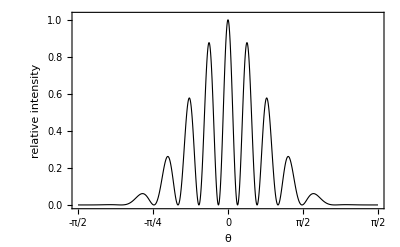

```mathematica
plotDEStheor=Plot[intensity[x Pi/180,1,(2Pi/myLambda),(myD*myLambda),myA*myLambda],{x,-90,90},
AxesOrigin -> {-90,0},
PlotRange->{{-90,90},{0,1.02}},
PlotStyle->{Black,Thickness[0.002]},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->16},
BaseStyle->{"Times",12},
Frame->{{True,False},{True,False}},
FrameLabel->{θ,"relative intensity"},
FrameTicks->{{Automatic,None},{{{-90,-π/2},{-45,-π/4},{0,0},{45,π/2},{90,π/2}},None}},
PerformanceGoal->"Quality"]
```

```mathematica
For[i=1,i≤7,i++,
plotDES[i]=Show[{plotDEStheor,plotDESlist[i]},ImageSize->400];
Export["plotDSEsample"<>ToString[i]<>".pdf",plotDES[i]]
]
```